# Video Traking UI

## User Interface for gereic video tracking problems

## Step 0 - Load the program

```mathematica
Quit[];
```

```mathematica
<<VideoTracking`
$HistoryLength = 2; (*prevent memory overload*)
SetOptions[FFmpeg, 
"Colors"->1 (*number of color channels*),"ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
];
SetOptions[VideoIO,
"FrameIdFromFrame"->False
];
```

## Step 1 - Select the video file

```mathematica
VideoSelect[ "/Users/kmisiunas/Dropbox/PhD/Software/video-tracking/practice_videos/brightfield_diffusion_channel_low_density_30fps.avi"]
```

brightfield_diffusion_channel_low_density_30fps.avi has 1333 frames and is 720x480

## Step 2 - Select region of intrest

```mathematica
ROISelect[]
```

(282 | 121
460 | 150)

```mathematica
ROISelect[({{282, 121}, {460, 150}})]
```

(282 | 121
460 | 150)

## Step 3 - Compute the background image

```mathematica
VideoBufferAll[]
```

Buffer: expected 1333 frames. ffmpeg found 1333

Buffer: loaded entire video

```mathematica
bg = UpdateBackgroung[1, VideoLength[]]
```

-Graphics-

#### BIG PROBLEM

```mathematica
ROIDimmensions[]
```

{178,29}

```mathematica
ImageDimensions@VideoGet@1
```

{178,29}

## Step 4 - configure tracing algorithm

```mathematica
VideoFindThreshold[]
```

```mathematica
Options[VideoTracking];

SetOptions[VideoTracking, 
 FilterCircularity -> {0.5, 1.6},
 FilterArea -> {7,50},
 UpdateBackgroung -> False,
 Threshold -> 0.090
]
```

{Threshold→0.09,FilterArea→{7,50},FilterCircularity→{0.5,1.6},AnalysisBlockSize→4000,UpdateBackgroung→False,BackgroundAlgorithm→SmartMeanBackground,MinThreshold→0.05}

```mathematica
(*avi filter: DV video*)
SetOptions[VideoTracking, 
 FilterCircularity -> {0.5, 1.5},
 FilterArea -> {6, 40},
 UpdateBackgroung -> False,
 Threshold -> 0.065
]
```

{Threshold→0.06,FilterArea→{6,40},FilterCircularity→{0.5,1.5},AnalysisBlockSize→4000,UpdateBackgroung→False,BackgroundAlgorithm→SmartMeanBackground,MinThreshold→0.05}

```mathematica
(*normal*)
SubstractBG[img_Image]:=ImageSubtract[ img, VideoTracking`Private`background]
```

```mathematica
(*for black particles*)
SubstractBG[img_Image]:=ImageDifference[img,VideoTracking`Private`background]
```

```mathematica
(*for black particles (experimental)*)
SubstractBG[img_Image]:=ImageSubtract[ 
ImageDifference[img,VideoTracking`Private`background],
ImageSubtract[ img, VideoTracking`Private`background]
]
```

## Step 5 - Inspect per frame basis (run many times!)

```mathematica
<<SubPixelFit`
```

(56.61 | 13.99 | 1. | 1.65 | 0.01 | 0.2
84.73 | 12.89 | 1. | 1.7 | 2.84 | 0.14)

-Graphics-

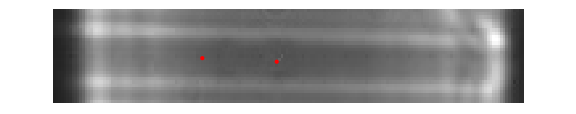

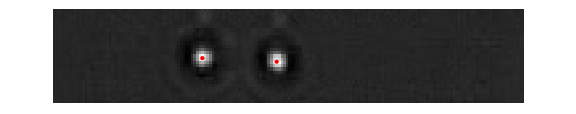

-Graphics-

Area→{1→33.75,2→36.5}

Circularity→{1→1.10163,2→1.08204}

```mathematica
frame =7 30+6;
If[0>frame||frame >  VideoLength[], frame = 1; Print@"Frame out of range. set to 1."];

ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list[[;;,{1,2}]]},ImageSize->Large]

curPos = AnalyseFrame[frame]

ShowTrackOverlayed[ VideoGet[frame] , curPos]
ShowTrackOverlayed[ CurrentBackground[], curPos]
ShowTrackOverlayed[ SubstractBG@VideoGet[frame] // ImageAdjust, curPos] 
ShowTrackOverlayed[ FrameBinarize@SubstractBG@VideoGet[frame] , curPos]

"Area"-> ComponentMeasurements[ FrameBinarize@SubstractBG@VideoGet[frame] ,"Area"]

"Circularity"-> ComponentMeasurements[ FrameBinarize@SubstractBG@VideoGet[frame] ,"Circularity"]
```

## Analyse many videos

```mathematica
ComputeVideo[file_] := Module[{loadTime, analysisTime,oldROI,outputFolder},
Clear[output];
Print@"==============================================";
oldROI = ROICurrent[] ; (*reuse ROI*)

Print @VideoSelect[ file ];

Print["Video lenght (30fps eqv.): "<> ToString@(VideoLength[] /30 // N) <> " sec"];
Print ["ROI: "<> ToString@ROISelect[ oldROI ]];

loadTime = AbsoluteTiming[
VideoBufferAll[];
Print @ UpdateBackgroung[1, VideoLength[] ] ;
(*Print @ ImageAdjust@ImageDifference[UpdateBackgroung[bg ],GetFrame[1]];*)
][[1]];

{analysisTime,output} = AbsoluteTiming @ RunAnalysis[1, NumberOfFrames[]];

Print[ "Analysis took (load + recognition): "<> ToString@loadTime <> " + "<> ToString@analysisTime<>" = "<> ToString@(loadTime+analysisTime)<>" sec"];
Print["Particles instances found: " <> ToString@Length@output ];

(*update time and positions to absolute ones*)
firstID = VideoFrameID@ GetRawFrames[1][[1]];
cornerPos = ROICurrent[]⟦4⟧;
output⟦All,1⟧ += (firstID-1); (*time*)
output⟦All,2⟧ += cornerPos⟦1⟧; (*x*)
output⟦All,3⟧ += cornerPos⟦2⟧; (*y*)

outputFolder = FileNameJoin[{DirectoryName[file],"raw_points"}];
If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

Print["Done: "<>
ToString@Export[ FileNameJoin[{outputFolder, (FileBaseName[file] <>".csv")}],  output]];
]
```

```mathematica
analyseTheseFiles = FileNames["low_conc_square_wave_(starts_+1V_on_right)2_*.avi","E:\\Experiments\\Antony\\2015-02-12\\",1][[1]]
```

E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s10.avi

```mathematica
analyseTheseFiles=("E:\\Experiments\\Antony\\2015-02-18\\3\\2015_02_18_square_wave_s"~~ToString@#~~".avi")&/@ {7}
```

{E:\Experiments\Antony\2015-02-18\3\2015_02_18_square_wave_s7.avi}

```mathematica
Do[ ComputeVideo[f], {f, analyseTheseFiles }]
```

==============================================

2015_02_18_square_wave_s7.avi has 12000 frames and is 400x400

Video lenght (30fps eqv.): 400. sec

ROI: {{141, 248}, {225, 248}, {225, 219}, {141, 219}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Analysis took (load + recognition): 32.510463 + 76.456706 = 108.96717 sec

Particles instances found: 2026

Done: E:\Experiments\Antony\2015-02-18\3\raw_points\2015_02_18_square_wave_s7.csv

#### Developing preview function

```mathematica
<<KLab`
```

```mathematica
Clear[track]
```

```mathematica
tracks = KLabImport["C:\\Users\\km558\\Dropbox\\PhD\\Projects\\Electrophoresis transport, 2014\\experiments\\antony\\2015-02-18\\3\\2015_02_18_square_wave_s7.json"]
```

KLab: Imported Track Assembly
experiment→from: /Users/kmisiunas/Dropbox/PhD/Projects/Electrophoresis transport, 2014/experiments/antony/2015-02-18/3/2015_02_18_square_wave_s7.csv
comment→
time→Mon 2 Mar 2015 20:50:53
units→{frame,px_x,px_y,px_z}
array_format→2
number→78
version→2

{0→{{2.27022×10^6,224.852,232.812},{2.27022×10^6,221.889,232.941},{2.27023×10^6,219.076,233.508},{2.27023×10^6,215.832,233.85},{2.27023×10^6,212.666,233.78},12,{2.27024×10^6,157.058,237.126},{2.27024×10^6,152.712,237.691},{2.27024×10^6,147.81,237.228},{2.27024×10^6,142.432,237.472}},76,79→{1}}
 |  |  |  |

```mathematica
FilterTrack[track_]:= Select[ track, id-50≤ #[[1]]≤ id &]

DrawTrack[track_]:= 
{RandomChoice[{Red, Blue, Green,Purple, Orange, Yellow} ] ,Opacity[0.5], Disk[ Select[track, #[[1]] == id&][[1,{2,3}]], 3], Line[track[[All, {2,3}]]]};
```

```mathematica
img = FFImport[ VideoFile[], {"Frames",9480+50+15}];
id = VideoFrameID[img];

drawSegments = Select[
FilterTrack/@(tracks[[All,2]]),
Length@#>0&];

"lead positions" -> Select[drawSegments, (Last@#)[[1]] == id&][[All,-1]]

Show[img,
Graphics[Flatten[ DrawTrack/@drawSegments, 1]],
ImageSize-> Large
]
```

lead positions→{{2.27282×10^6,145.11,238.522},{2.27282×10^6,166.607,236.223},{2.27282×10^6,206.959,234.174},{2.27282×10^6,183.554,235.149}}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

Away by X:
+2px, +2px,+1,5px, +2.5